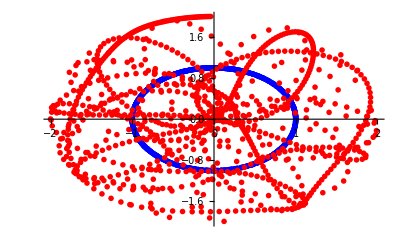

```mathematica
(* Here is our function to create the Bashforth-Adams approximation. uPast and thetaPast are the prior/(n-1) values. *)

(*Also, we used Euler approximation to generate the intial conditions. *)

tt=0; δt=0.01;niter= 1000;k=10; mOne = 1; mTwo = 1; lOne = 1; lTwo = 1; g = 9.8;

(* Here we created fuctions for all of the a's. *)
aOne[θ_, φ_] := ( 
g(4*mOne + 5*mTwo)Sin[θ]
);
aTwo[θ_, φ_]:= (
 3*g*mTwo*Sin[θ - 2*φ]
);
aThree[θ_, φ_, u_] := (
 3*lOne*mTwo*Sin[2(θ - φ)](u)^2  (* uOne*)
);
aFour[θ_, φ_, u_] := (
4*lTwo*mTwo*Sin[θ -φ](u)^2 (* uTwo *)
);
aFive[θ_, φ_] := (
3*g(mOne + 2*mTwo)Sin[2*θ - φ]
);
aSix[θ_, φ_] := (
g(mOne + 6*mTwo)Sin[φ]
);
aSeven[θ_, φ_, u_]:= (
4*lOne(mOne + 3*mTwo)Sin[θ - φ](u)^2 (* uOne *)
);
aEight[θ_, φ_, u_]:= (
3*lTwo*mTwo*Sin[2(θ - φ)](u)^2 (* uTwo *)
);


(* Now creating functions for uOne and uTwo, named fOne and fTwo to avoid confusing with variables. *)
fOne[θ_, φ_ , u1_, u2_ ] :=(
(-3(aOne[θ, φ]+ aTwo[θ, φ]  + aThree[θ, φ, u1] + aFour[θ, φ, u2]))/(lOne(8*mOne + 15*mTwo - 9*mTwo*Cos[2(θ - φ)]))
);
fTwo[θ_, φ_ , u1_, u2_] := (
(3(aFive[θ, φ ] - aSix[θ, φ]+ aSeven[θ, φ , u1] + aEight[θ, φ , u2]))/(lTwo(8*mOne + 15mTwo - 9*mTwo*Cos[2(θ - φ)]))
);

(* Initial conditions *)
thetaOnePast = π; uOnePast = 1; thetaTwoPast = π ; uTwoPast = 1; 
thetaOne=thetaOnePast +δt uOnePast;
thetaTwo=thetaTwoPast +δt uTwoPast;
uOne =uOnePast -δt*fOne[thetaOnePast, thetaTwoPast, uOnePast, uTwoPast];
uTwo = uTwoPast - δt*fTwo[thetaOnePast, thetaTwoPast, uOnePast, uTwoPast];

rrDP=Reap[
Do[

(* Update θ here *)
utempOne=uOne;
utempTwo = uTwo;

uOne += (3/2)δt*fOne[thetaOne, thetaTwo, utempOne, utempTwo] - (1/2)δt*fOne[thetaOnePast, thetaTwoPast, uOnePast, uTwoPast];

uTwo += (3/2)δt*fTwo[thetaOne, thetaTwo, utempOne, utempTwo] - (1/2)δt*fTwo[thetaOnePast, thetaTwoPast, uOnePast, uTwoPast];
thetaOne +=  (3/2)(δt*utempOne) - (1/2)(δt*uOnePast);
thetaTwo += (3/2)(δt*utempTwo) - (1/2)(δt*uTwoPast);

tt+= δt; (* Update t *)
thetaOnePast = thetaOne;
thetaTwoPast = thetaTwo;
uOnePast = utempOne;
uTwoPast = utempTwo;

Sow[{tt,thetaOne, thetaTwo}]; (* Output *)

,{i,niter}]
];

(* Getting the thetas from the rrDP results *)
t1 = Table[rrDP[[ 2, 1, i, 2]],{i, niter}];
t2 = Table[rrDP[[ 2, 1, i, 3]],{i, niter}];

(* getting the (x,y) coordinates based on theta1 or theta2 *)
x1=Table[{lOne Sin[t1[[i]]],-lOne Cos[t1[[i]]]}, {i, niter}];
x2=Table[{x1[[ i, 1]] + lTwo  Sin[t2[[i]]],x1[[i, 2]] -lTwo Cos[t2[[i]]]}, {i, niter}];

(* Plot of the path of the ends of each rod *)
marker1=Graphics[{Blue,Disk[]}];
marker2=Graphics[{Red,Disk[]}];
p1 = ListPlot[x1,PlotMarkers->{marker1, .03}, PlotRange->{{-1,1},{-1,1}}];
p2 = ListPlot[x2, PlotMarkers-> {marker2, .03}];
Show[p1, p2, PlotRange -> {{-2, 2},{-2, 2}}]
```

```mathematica
(* Pendulum animation - notice how it speeds up as time increases, this is due to the overestimation of the Bashford-Adams approximation *)
Animate[
Graphics[{
Point[x1[[i]]],
Point[x2[[i]]], 
Line[{{0,0},x1[[i]]}],
Line[{x1[[i]],x2[[i]]}]},
  PlotRange->{{-2,2},{-2,2}}
],
{i, 1 , niter,1},
 AnimationRate->100
]
```